# Les polynômes orthogonales

## Formule de Rodrigues - Les polynômes de Jacobi P_n^(α,β)(x) - Les polynômes de Legendre nx

```mathematica
Clear["Global`*"]
```

Les polynômes de Jacobi, notés P_n^(α,β)(x)sont, P_0^(α,β)(x),P_1^(α,β)(x),P_2^(α,β)(x),...,P_k^(α,β)(x). Dans cette notation α>-1 et β>-1sont des nombres réels . Pour trouver les  polynômes de Legendrenx, on doit choisir α=0 et β=0 :

```mathematica
k:=3
```

```mathematica
α:=0
```

```mathematica
β:=0
```

## Formule de Rodrigues

Les polynômes de Legendre peut être définie par la formule de Rodrigues :

```mathematica
P[n_,α_,β_,x_]:=1/(K[n] w[x])D[(w[x] g[x]^n), {x,n}]
```

### Initiation

```mathematica
table={{"Polynôme de degré 0, 1, ou 2", g[x_]=1-x^2}, {"Fonction poids", w[x_]=(1-x)^α(1+x)^β}, {"Limite gauche d'intervalle d'orthogonalité", a=-1}, {"Limite droite d'intervalle d'orthogonalité", b=+1}, {"Multiplicateur de standardisation", K[n_]=(-1)^n 2^n n!}, {"Coefficient de x", κ[n_]=(2^n Gamma[n+1/2])/(n!Gamma[1/2])}, {"Odre", k:=3}};
```

## Les polynômes

```mathematica
TableForm[Table[{n,P[n,α,β,x]},{n,0,k}]//Simplify,TableAlignments->Left,TableSpacing->{3,5},TableHeadings->{None,{"n","P[n,α,β,x]"}}]
```

n | P[n,α,β,x]
0 | 1
1 | x
2 | 1/2 (-1+3 x^2)
3 | 1/2 x (-3+5 x^2)

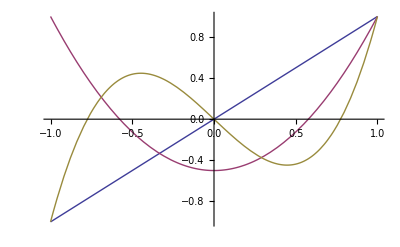

```mathematica
Plot[Evaluate[Table[P[n,α,β,x],{n,k}]],{x,-1,1}]
```

## Orthogonalité

```mathematica
Table[∫_a^b w[x]P[n,α,β,x]P[n',α,β,x]ⅆx,{n,0,k},{n',0,k}]//TableForm
```

2 | 0 | 0 | 0
0 | 2/3 | 0 | 0
0 | 0 | 2/5 | 0
0 | 0 | 0 | 2/7

#### Carré de la norme

```mathematica
h[n_]=(2^(α+β+1)Gamma[n+α+1]Gamma[n+β+1])/((2n+α+β+1)n!Gamma[n+α+β+1])
```

(2 Gamma[1+n])/((1+2 n) n!)

```mathematica
Table[h[n] KroneckerDelta[n,n'],{n,0,k},{n',0,k}]//TableForm
```

2 | 0 | 0 | 0
0 | 2/3 | 0 | 0
0 | 0 | 2/5 | 0
0 | 0 | 0 | 2/7

## Normalization

```mathematica
P̃[n_,α_,β_,x_]:=P[n,α,β,x]/(√h[n])
```

```mathematica
TableForm[Table[{n,P̃[n,α,β,x]},{n,0,k}]//Simplify,TableAlignments->Left,TableSpacing->{3,5},TableHeadings->{None,{"n","P̃[n,α,β,x]"}}]
```

n | P̃[n,α,β,x]
0 | 1/(√2)
1 | √(3/2) x
2 | 1/2 √(5/2) (-1+3 x^2)
3 | 1/2 √(7/2) x (-3+5 x^2)

## Orthonormalité

```mathematica
Table[∫_a^b w[x]P̃[n,α,β,x]P̃[n',α,β,x]ⅆx,{n,0,k},{n',0,k}]//TableForm
```

1 | 0 | 0 | 0
0 | 1 | 0 | 0
0 | 0 | 1 | 0
0 | 0 | 0 | 1

```mathematica
Table[KroneckerDelta[n,n'],{n,0,k},{n',0,k}]//TableForm
```

1 | 0 | 0 | 0
0 | 1 | 0 | 0
0 | 0 | 1 | 0
0 | 0 | 0 | 1

## Développement de la fonction f(x)

### La fonction à développer

```mathematica
f[x_] := Abs[x]
```

### Les coéfficients

```mathematica
Subscript[a, n_]:=∫_a^b w[x]P̃[n,α,β,x]f[x]ⅆx
```

```mathematica
Table[Subscript[a, n],{n,0,k}]
```

{1/(√2),0,(√(5/2))/4,0}

### Développement

```mathematica
fdev[x_]:=∑_(n=0)^5 Subscript[a, n] P̃[n,α,β,x]
```

## Représentation

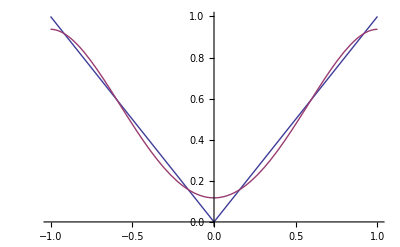

```mathematica
Plot[Evaluate[{f[x],fdev[x]}],{x,-1,1},PlotRange->All]
```

```mathematica
Manipulate[Plot[Evaluate[{f[x],∑_(n=0)^k Subscript[a, n] P̃[n,α,β,x]}],{x,-1,1},PlotRange->All],{k,1,10,1},ControlType->Setter]
```

## EDP

```mathematica
λ[n_]=n(K[1]D[P[1,α,β,x], {x,1}]+1/2(n-1)D[g, {x,2}](x))
```

-2 n

Le n - ième polynôme de Laguerre satisfait l' équation différentielle suivante :

```mathematica
EDP=(D[(w[x] g[x]D[u[x], x]), x]-λ[n] w[x]u[x])/w[x]==0//FullSimplify
```

2 n u[x]==2 x u'[x]+(-1+x^2) u''[x]

```mathematica
DSolve[EDP,u[x],x]
```

{{u[x]→C[1] LegendreP[1/2 (-1+√(1+8 n)),x]+C[2] LegendreQ[1/2 (-1+√(1+8 n)),x]}}

```mathematica
TableForm[Table[{n,P[n,α,β,x],JacobiP[n,α,β,x],LegendreP[n,x]},{n,0,k}]//Simplify,TableSpacing->{3,5},TableHeadings->{None,{"n","P[n,α,β,x]","JacobiP[n,α,β,x]","LegendreP[n,x]"}}]
```

n | P[n,α,β,x] | JacobiP[n,α,β,x] | LegendreP[n,x]
0 | 1 | 1 | 1
1 | x | x | x
2 | 1/2 (-1+3 x^2) | 1/2 (-1+3 x^2) | 1/2 (-1+3 x^2)
3 | 1/2 x (-3+5 x^2) | 1/2 x (-3+5 x^2) | 1/2 x (-3+5 x^2)